```mathematica
<<GranSimTools`
```

```mathematica
<<disLocate`
```

```mathematica
<<StandardPolyLib`
```

```mathematica
(*  Inflates the Polygons to OverlapScale % times bigger  *)
(*  ------------------------------------------------------  *)
Inflate2=Compile[{{Rcurrent,_Real,2},{poly,_Real,2},{SimStep,_Real},{GrowthRate,_Real},{OverlapScale,_Real}},
Block[{inflatedPolys,rot,OverlapScaleSize,M},

OverlapScaleSize = SimStep*GrowthRate*OverlapScale;

inflatedPolys=Table[
rot = Rcurrent[[n,3]];
M={{Cos[rot], -Sin[rot]},{Sin[rot],Cos[rot]}};
Table[
((M.poly[[j]])*OverlapScaleSize)+{Rcurrent[[n,1]],Rcurrent[[n,2]]}
,{j,1,Length[poly],1}]
,{n,1,Length[Rcurrent],1}];

inflatedPolys
] ,CompilationTarget->"C"];
```

```mathematica
Table[colF[x],{x,1,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[colF]
colF[x_]:=Part[{
(*RGBColor[{255,51,51}/256],*)(*bjorn red*)
Orange,
RGBColor[30/256,144/256,255/256],


-Graphics-,
RGBColor[0.545,0.0,0.8],
Red,
Yellow,
RGBColor[{0,153,51}/256],
RGBColor[{51,51,153}/256],

(*RGBColor[0.545,0.0,0.8],*) (*bjorn orange*)
RGBColor[{0,153,51}/256], (*bjorn green*)
(*RGBColor[147/255,3/255,46/255]*)
(*Yellow*)
Blue
(*RGBColor[{51,51,153}/256]*)(*bjorn blue*)
},x];
```

```mathematica
tag="data/bone/"
(*tag="data/DIP-CuPc-(1-0)-60n/"*)
(*tag="data/Interactions-pbc/"*)

dir = "/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/"<>tag


polygonDir[x_]:= dir<>"meta/simulation_obj/particle_"<>ToString[x]<>".dat"
(*initDir=dir<>"Rcurrent/Init.dat"*)
rcurrentDir=dir<>"conf/conf_1_466.dat"
boxDir=dir<>"meta/simulation_box/container.dat";

(*initRcurrent=Import[initDir,"Table"];*)
Rcurrent = Import[rcurrentDir,"Table"];
{simstep,growthRate, pf, cpuTime} =Rcurrent[[1]]
Rcurrent=Rcurrent[[2;;]];
(*{{simstep,growthRate,overlap}} = Import[dir<>"Rcurrent/Rsimstep.dat","Table"]*)
numPolys=Max[Rcurrent[[2;;,4]]  ];
polys=Table[{},{x,1,numPolys }];
polys=Table[Import[polygonDir[x], "Table"],{x,1,numPolys }];
boxo= Import[boxDir,"Table"];

rand=Import[dir<>"conf/RandomRolls.dat","Table"];
```

data/bone/

/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/bone/

/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/bone/conf/conf_1_466.dat

{466,0.00001,0.00477834,0.322213}

Import::nffil: File not found during Import.

```mathematica
Clear[show]
```

```mathematica
(*timing = 99086sec, 259 steps*)
(*timing = 2997sec, 160 steps*)
(*mkl removed *)
(*timing = 642sec,   81 steps*)
(*timing = 3155sec,   209 steps*)
(*timing = 13899sec,   259 steps*)
```

```mathematica
colours={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
Render2[a_,b_]:=Show@Graphics[{b,EdgeForm[Thick],Polygon[a]}];
q= Table[(Cos[Pi/6]/2   {Cos[x+Pi/6],Sin[x+Pi/6],0})(*+{0.5,0.5,0}*),{x,2Pi/6,2.Pi,2Pi/6}];
p={{1.,0.5},{0.75,0.933013},{0.25,0.933013},{0.,0.5},{0.25,0.0669873},{0.75,0.0669873},{1.,0.5}};
```

```mathematica
show:=(
Rcurrent = Import[rcurrentDir,"Table"];
{simstep,growthRate, pf, cpuTime} =Rcurrent[[1]];
Rcurrent=Rcurrent[[2;;]];
rand=Import[dir<>"conf/RandomRolls.dat","Table"];

Show[{
(*Show@Table[Render[inf[[x]],colF[Rcurrent[[x,4]]]],{x,Range@Length@Rcurrent[[;;,4]]}]*)
(*ListPlot[inf,Joined->True,Axes->True]*)
(*ListPlot[rand+ Table[Rcurrent[[1,1;;2]],{x,1,Length[rand]}],PlotStyle->{Black,Opacity[0.5],PointSize[Small]}]*)
(*PolydisperseFinalConfiguration[Rcurrent,polys,simstep,growthRate, box]*)

(*Graphics[{White,Opacity[1.0],Polygon[boxo]}],*)



(*   ---- Square Periodic Boundary ---- *)
Graphics[{Thick,Black,Line[boxo]}],
(*Table[
Render2[Inflate2[{Flatten[{#,k}]}, polys[[k]], simstep,growthRate  ,1],Directive[Opacity[0.5],colF[k]]]&/@ApplyPeriodicBoundary[Select[Rcurrent,#[[4]]==k&][[All,1;;3]],closedBindingBox,SetDistance->1,ReturnDim->3]
,{k,1,Max[Rcurrent[[;;,4]]]}],*)


(*   ---- Hexagonal Periodic Boundary ---- *)
(*Graphics[{Thin,Black,Line[boxo]}],
Table[
Table[Render2[Inflate2[{Flatten[{#+ pbc,k}]}, polys[[k]], simstep,growthRate  ,1],Directive[Opacity[0.33],colF[k]]],{pbc,q}]&/@Select[Rcurrent,#[[4]]==k&][[All,1;;3]]
,{k,1,Max[Rcurrent[[;;,4]]]}],*)


(*Show[Graphics[{Opacity[1],Point/@(Rcurrent[[1,1;;2]]+#&/@rand[[;;,1;;2]])}]],
*)

(*PolydisperseFinalConfiguration[

Flatten[{#,1}]&/@ApplyPeriodicBoundary[Rcurrent[[;;,1;;3]],closedBindingBox,SetDistance->0.5,ReturnDim->3]

,polys,simstep,growthRate, boxo],*)


(*Render[Inflate2[Rcurrent[[1,1;;3]]+#&/@rand[[;;]], polys[[1]], simstep,growthRate  ,1],Black],*)




Table[
Render2[Inflate2[{Flatten[{#,k}]}, polys[[k]], simstep,growthRate  ,1],Directive[Opacity[1],colF[k]]]&/@Select[Rcurrent,#[[4]]==k&][[All,1;;3]]
,{k,1,Max[Rcurrent[[;;,4]]]}]









(*Render2[Inflate2[{Rcurrent[[1]]}, polys[[1]], simstep,growthRate  ,1],Black]*)
(*,Show[Graphics[{Opacity[0.21],Point/@(Rcurrent[[1,1;;2]]+#&/@rand[[;;,1;;2]])}]]*)


}]);
```

Import::nffil: File not found during Import.

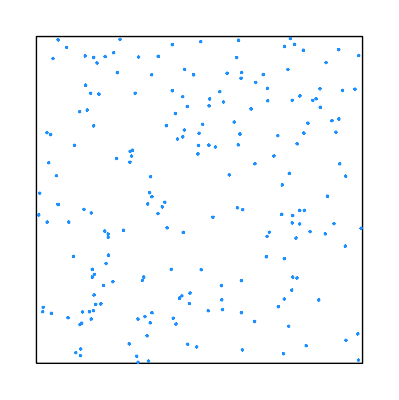

```mathematica
show
```

Import::nffil: File not found during Import.

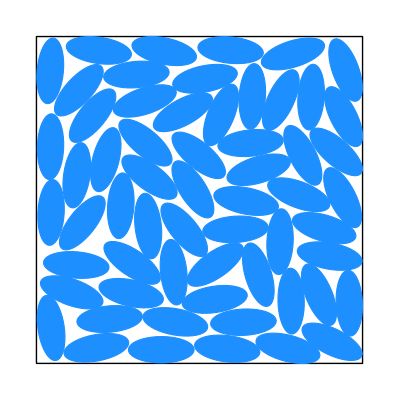

```mathematica
show120=show
```

Import::nffil: File not found during Import.

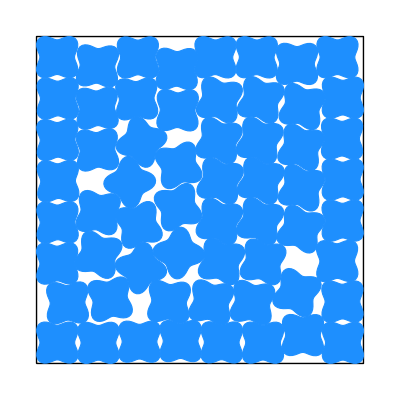

```mathematica
show021=show
```

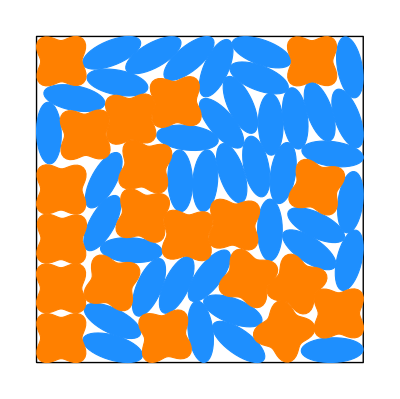

```mathematica
show221
```

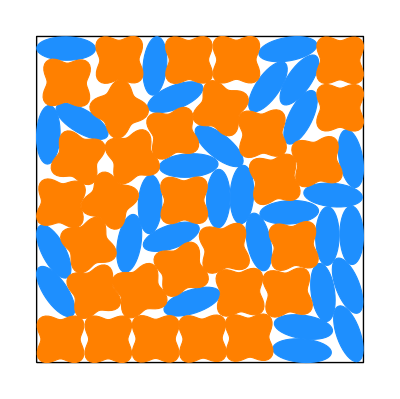

```mathematica
show121
```

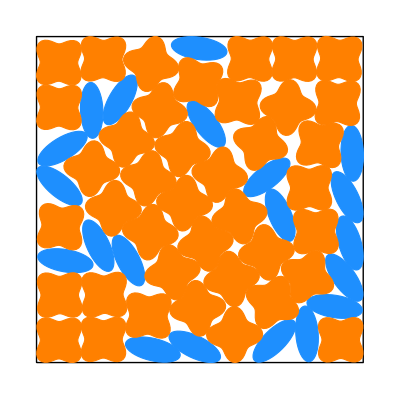

```mathematica
show122
```

```mathematica
show
```

Import::nffil: File not found during Import.

-Graphics-

Import::nffil: File not found during Import.

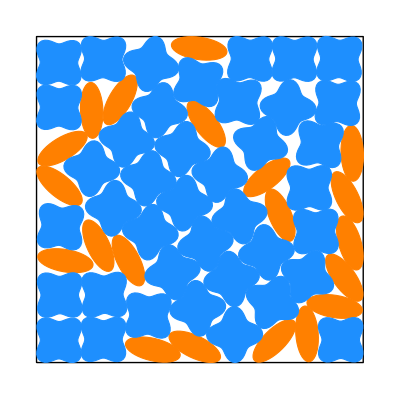

```mathematica
show
```

Set::shape: Lists {simstep, growthRate} and {8993, 0.00001, 0.841455, 1852.95} are not the same shape.

Import::nffil: File not found during Import.

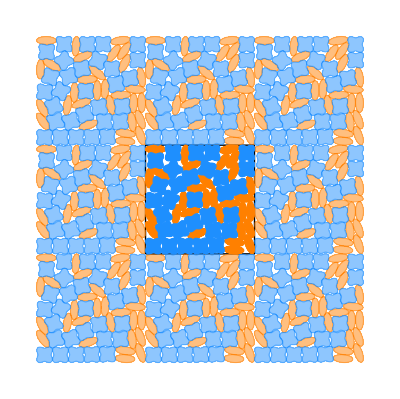

```mathematica
Show[{show}(*,PlotRange-> {{-1,2},{-0.37,1.37}}*)]
```

```mathematica
Export["/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/Interactions-pbc/meta/simulation_box/Polydisperse_Interactions_SquarePBC_4096beads_(noedge).jpeg",Show[{show},PlotRange-> {{-0.1,1.1},{-0.1,1.1}}(*PlotRange-> {{-1,2},{-0.37,1.37}}*)],(*ImageSize->1500,*)ImageResolution->1200]
```

/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/Interactions-pbc/meta/simulation_box/Polydisperse_Interactions_SquarePBC_4096beads_(noedge).jpeg

```mathematica
(*Export["/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/McMaster-Fireball-Pheonix/meta/simulation_box/Logo_McMaster-FireBall-Pheonix_(soft).jpeg",show,(*ImageSize->1500,*)ImageResolution->1200]*)
```

/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/McMaster-Fireball-Pheonix/meta/simulation_box/Logo_McMaster-FireBall-Pheonix_(soft).jpeg

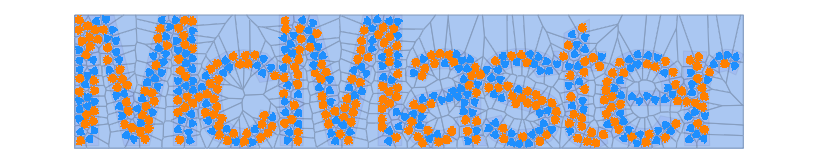

```mathematica
Show[{VoronoiMesh[Rcurrent[[All,1;;2]],{Min@#,Max@#}&/@{boxo[[;;,1]],boxo[[;;,2]]}],
Render[boxo,Directive[{Opacity[0]}]],
PolydisperseFinalConfiguration[Rcurrent,polys,simstep,growthRate, boxo]
}]
```

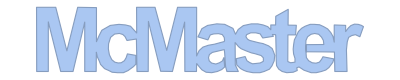

```mathematica
MeshRegion[boxo,Polygon[Range@Length@boxo]]
```

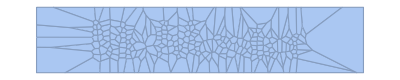

```mathematica
VoronoiMesh[Rcurrent[[All,1;;2]]]
```

```mathematica
{Min@#,Max@#}&/@{boxo[[;;,1]],boxo[[;;,2]]}
```

{{-0.861415,0.995726},{-0.161292,0.198706}}

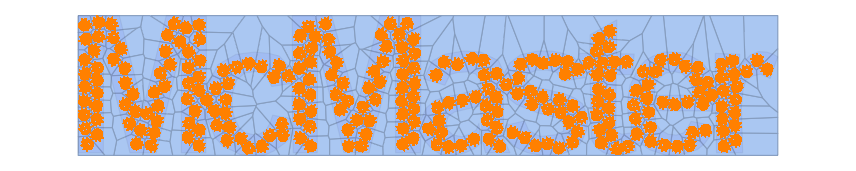

```mathematica
Show[{VoronoiMesh[Rcurrent[[All,1;;2]],{Min@#,Max@#}&/@{boxo[[;;,1]],boxo[[;;,2]]}],
Render[boxo,Directive[{Opacity[0]}]],
PolydisperseFinalConfiguration[Rcurrent,polys,simstep,growthRate, boxo]
}]
```

```mathematica
Dynamic[Refresh[show,UpdateInterval->2]]
```

```mathematica
(*
Dynamic[
Refresh[
lastModified=FileDate[rcurrentDir,"Modification"],
updatedQ:=With[{modificationDate=FileDate[rcurrentDir,"Modification"]},If[lastModified==modificationDate,False,lastModified=modificationDate;True]];
If[updatedQ,
Rcurrent = Import[rcurrentDir,"Table"];
{simstep,growthRate} =Rcurrent[[1]];
Rcurrent=Rcurrent[[2;;]];
##&[]
,
##&[]
]
,UpdateInterval->5]
]*)
```

{890,0.0001}

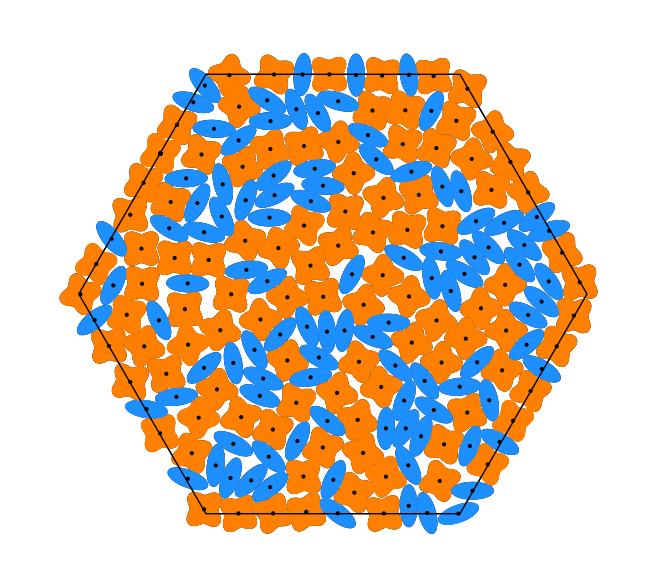

```mathematica
Rcurrent2Pen1CuPc=Rcurrent;
{simstep2Pen1CuPc,growthRate2Pen1CuPc} ={simstep,growthRate}
```

Show::gcomb: Could not combine the graphics objects in Show[{« 1 »}].

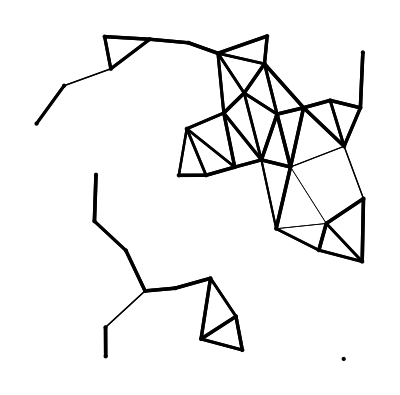
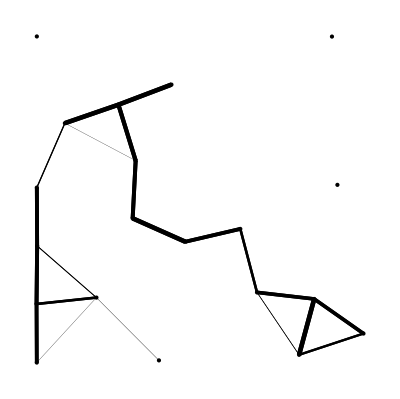

```mathematica
pt=Table[
DeleteCases[If[Rcurrent[[#,4]]==x,#]&/@Range[Length[Rcurrent]],Null]
,{x,1,Length[polys]}];

Table[OverlapNetwork[Rcurrent[[#,1;;3]]&/@pt[[shapeN]],polys[[shapeN]],simstep, growthRate,1.3,box],{shapeN,1,2}]
```

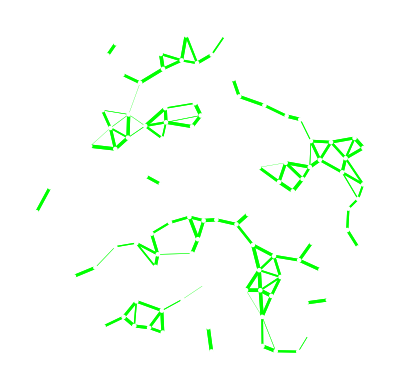

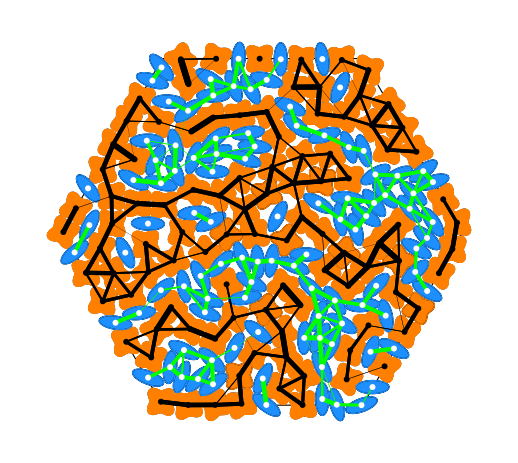

```mathematica
shapeN=1;
(*back=Render[box,RGBColor[{92,10,12}/256]]*)
b=Table[OverlapNetwork[Rcurrent[[#,1;;3]]&/@pt[[shapeN]],polys[[shapeN]],simstep, growthRate,1.3,box],{shapeN,{2}}]
Show[{ob,a,b}]
```

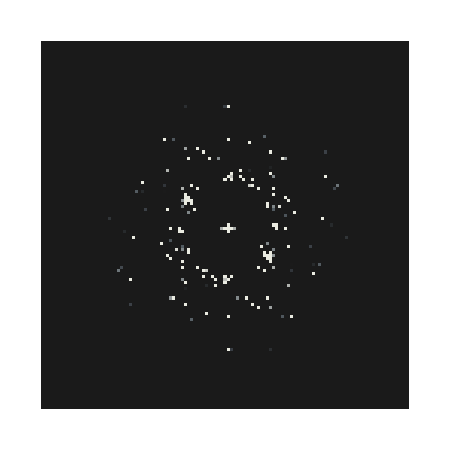

```mathematica
rc1=Rcurrent;
ss1=simstep;
DiffractionPatternFromPosition[Rcurrent[[;;,1;;2]]]
```

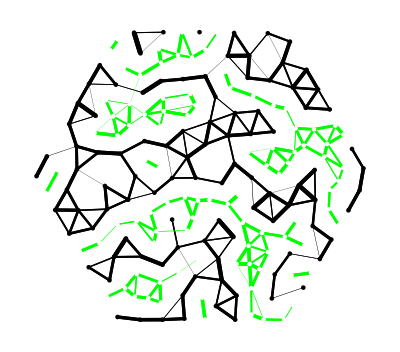

```mathematica
Show[{a,b}]
```

```mathematica
Clear[PairCorrelationFunction]
```

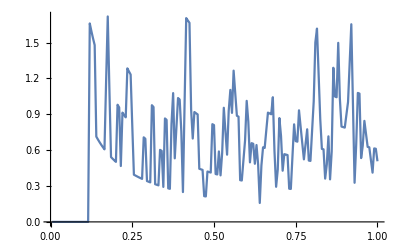

```mathematica
ListPlot[PairCorrelationFunction[Rcurrent,0.005,200],Joined->True]
```

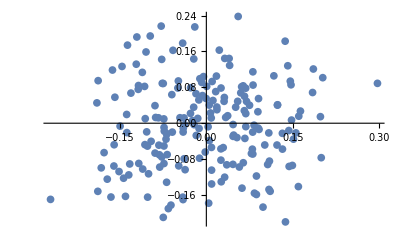

```mathematica
ListPlot[rand]
```

```mathematica
PolyArea[inf[[1]]]/(10^6)
```

1.80851×10^-8

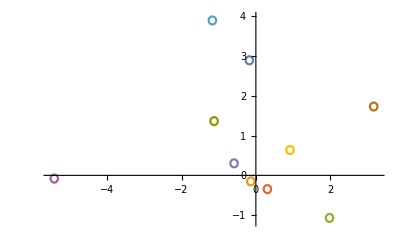

```mathematica
Inflate[Rcurrent[[#,1;;3]]&/@pt[[1]], polys[[1]], 10000  ,10^-5,1];
ListPlot[%,Joined->True]
```

```mathematica
Histogram[Rcurrent[[;;,3]]]
```

```mathematica
ListPlot[polys]
```

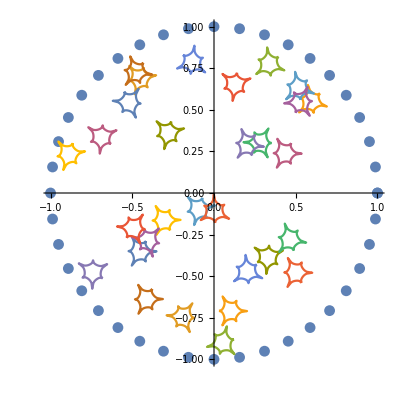

```mathematica
pt=Table[
DeleteCases[If[Rcurrent[[#,4]]==x,#]&/@Range[Length[Rcurrent]],Null]
,{x,1,Length[polys]}];
inf=Flatten[Table[Inflate[Rcurrent[[#,1;;3]]&/@pt[[x]], polys[[2]], simstep,growthRate  ,1],{x,1,Length[pt]}],1];
Show[{ListPlot[box,AspectRatio->1],
ListPlot[inf,Joined->True,Axes->True]}]
```

```mathematica
26*3
```

78

```mathematica
PolyArea[(0.0001 40000)polys[[1]]]
```

27.4697

```mathematica
(*  Inflates the Polygons to OverlapScale % times bigger  *)
(*  ------------------------------------------------------  *)



OverlapNetwork[pointPattern2D_,polygon_, Grow_,GrowthRate_,inflateRatio_,box_, Args___]:=
Block[{polys, nearestN,finalOverlapPolys,finalPolyAreas,numNear,overlapByPoly,npoints,maxLine,fullLinesToNearestN,finalSize,finalPlot,centerPoints},
If[Length[Grow]==0,finalSize=Grow,finalSize=First[Grow]];
polys = Inflate[pointPattern2D, polygon, finalSize,GrowthRate,inflateRatio];
nearestN=FindNearestForOverlap[pointPattern2D];
finalOverlapPolys=PolygonsThatOverlap[polys,nearestN];
(*finalPolyAreas =PolyArea[finalOverlapPolys[[#]]]&/@ Range[Length[finalOverlapPolys]];*)
finalPolyAreas=Table[PolyArea[finalOverlapPolys[[x]]],{x,1,Length[finalOverlapPolys],1}];


numNear=Length[nearestN[[1]]];
npoints=Length[pointPattern2D];
overlapByPoly={};
overlapByPoly = Table[{finalPolyAreas[[(x numNear)+#]]}&/@Range[numNear],{x,0,npoints-1,1}];

(*overlapByPoly = Table[{PolyArea[finalOverlapPolys[[(x numNear)+#]]]}&/@Range[numNear],{x,0,npoints-1,1}];*)

maxLine=PolyArea[polygon* GrowthRate*finalSize];

fullLinesToNearestN = Table[
If[Part[overlapByPoly[[const,#]],1]≠0.0,
Graphics[{Thickness[0.03Part[overlapByPoly[[const,#]],1]/maxLine],
Black(*ForceOverlapColourCode[Part[overlapByPoly[[const,#]],1]/maxLine]*),Line[{pointPattern2D[[const,1;;2]],pointPattern2D[[nearestN[[const,#]],1;;2]]}]}]
, Graphics[{Black,Opacity[0.0],Point[pointPattern2D[[const,1;;2]]]}]
]&/@Range[numNear]
,{const,1,npoints}];


centerPoints = Table[Graphics[{Black,(*PointSize[0.1 GrowthRate*finalSize],*)Point[pointPattern2D[[const,1;;2]]]  }],{const,1,npoints}];



(*Show[fullLinesToNearestN];*)


(*Show[{PlotFinalConfiguration[pointPattern2D,polygon, finalSize,GrowthRate,box,"automatic"],fullLinesToNearestN}]*)

If[Args===Null,finalPlot = Show[{PlotFinalConfiguration[pointPattern2D,polygon, finalSize,GrowthRate,box,"STM"],fullLinesToNearestN,centerPoints}]; ];

finalPlot = Show[{fullLinesToNearestN,centerPoints}];

If[Args=!=Null,
If[ToUpperCase[Args[[1]]]=="BOPVORONOI",
finalPlot = Show[{PlotVoronoiBOPcells[pointPattern2D,bindingBox, Args[[2]], "pbc" ],fullLinesToNearestN,centerPoints}];
];
];

finalPlot

];



(*LEGACY CODE*)

(*OverlapNetwork=Function[{pointPattern2D,polygon, Grow,GrowthRate,inflateRatio,box},

Block[{polys, nearestN,finalOverlapPolys,finalPolyAreas,numNear,overlapByPoly,npoints,maxLine,fullLinesToNearestN,finalSize},
If[Length[Grow]==0,finalSize=Grow,finalSize=First[Grow]];
polys = Inflate[pointPattern2D, polygon, finalSize,GrowthRate,inflateRatio];
nearestN=FindNearestForOverlap[pointPattern2D];
finalOverlapPolys=PolygonsThatOverlap[polys,nearestN];
(*finalPolyAreas =PolyArea[finalOverlapPolys[[#]]]&/@ Range[Length[finalOverlapPolys]];*)
finalPolyAreas=Table[PolyArea[finalOverlapPolys[[x]]],{x,1,Length[finalOverlapPolys],1}];


numNear=Length[nearestN[[1]]];
npoints=Length[pointPattern2D];
overlapByPoly={};
overlapByPoly = Table[{finalPolyAreas[[(x numNear)+#]]}&/@Range[numNear],{x,0,npoints-1,1}];

(*overlapByPoly = Table[{PolyArea[finalOverlapPolys[[(x numNear)+#]]]}&/@Range[numNear],{x,0,npoints-1,1}];*)

maxLine=PolyArea[polygon* GrowthRate*finalSize];

fullLinesToNearestN = Table[
If[Part[overlapByPoly[[const,#]],1]≠0.0,
Graphics[{Thickness[0.01Part[overlapByPoly[[const,#]],1]/maxLine],
ForceOverlapColourCode[Part[overlapByPoly[[const,#]],1]/maxLine],Line[{pointPattern2D[[const,1;;2]],pointPattern2D[[nearestN[[const,#]],1;;2]]}]}],
Graphics[{Black,Point[pointPattern2D[[const,1;;2]]]}]
]&/@Range[numNear]
,{const,1,npoints}];



(*Show[fullLinesToNearestN];*)
(*Show[{PlotFinalConfiguration[pointPattern2D,polygon, finalSize,GrowthRate,box,"automatic"],fullLinesToNearestN}]*)

Show[{PlotFinalConfiguration[pointPattern2D,polygon, finalSize,GrowthRate,box,"automatic"],fullLinesToNearestN}]

]];*)
(*]*)
```

```mathematica
(* Animation *)
```

```mathematica
SetDirectory["/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/bone/conf/"];
```

/Users/Arby_Bc/Dropbox/ThesisDropbox/Morphologies/morphologies/3_data/data/bone/conf

```mathematica
Length@FileNames[]
rc=Import[#,"Table"]&/@FileNames[];
```

282

```mathematica
sortedRc=SortBy[rc,#[[1,1]]&];
```

```mathematica
rcList=sortedRc[[All,2;;]];
firstline=sortedRc[[All,1]];
simstep=sortedRc[[All,1,1]]
growthRate=firstline[[1,2]]
```

{12,20,22,25,34,44,48,52,54,64,65,71,80,87,92,94,103,104,109,112,118,128,133,138,142,143,158,170,174,176,177,178,180,181,184,185,188,193,194,195,197,201,202,204,205,206,208,212,213,214,215,220,221,223,224,225,232,237,238,239,241,242,248,249,250,251,253,256,257,259,260,261,263,266,269,272,273,275,277,279,280,285,286,288,289,290,292,294,295,296,297,298,299,300,302,303,304,305,306,307,308,309,311,312,313,315,318,321,322,323,324,326,327,329,332,333,335,336,337,338,339,341,343,344,345,346,347,348,350,351,352,353,354,356,357,358,359,361,362,363,364,365,366,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508}

0.0001

```mathematica
animate[rc_ ,  simstep_ ] :=(i=0; Table[i++;
Show[{
Graphics[{Thick,Black,Line[boxo]}],
Table[
Render2[Inflate2[{Flatten[{#,k}]}, polys[[k]], simstep[[i]],growthRate  ,1],Directive[Opacity[1],colF[k]]]&/@Select[Rcurrent,#[[4]]==k&][[All,1;;3]]
,{k,1,Max[Rcurrent[[;;,4]]]}]
}]
,{Rcurrent,  rc}])
```

```mathematica
frames= animate[rcList,simstep];
```

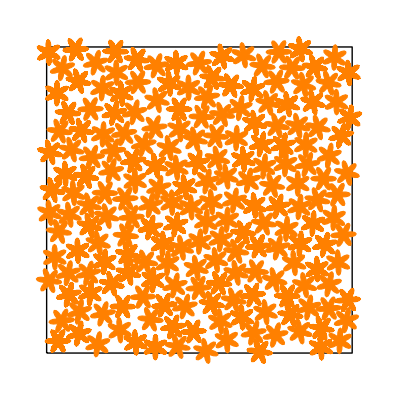

```mathematica
frames[[-1]]
```